Fit parameter:  P_π = 2.944 W  (RF power where this model predicts η=1)

R^2 = 0.945597

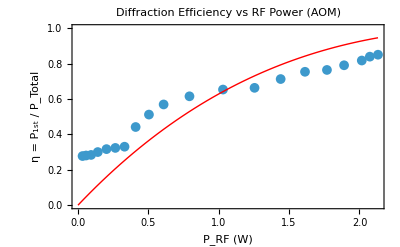

```mathematica
ClearAll["Global`*"];

prfEta={{0.0324,0.277672201},{0.0576,0.280836531},{0.093025,0.284018789},{0.140625,0.300199003},{0.2025,0.316827423},{0.265225,0.323604288},{0.330625,0.330452867},{0.4096,0.441787085},{0.5041,0.512038797},{0.6084,0.569256696},{0.7921,0.61533221},{1.030225,0.653483452},{1.2544,0.663200545},{1.44,0.712861702},{1.6129,0.753881459},{1.7689,0.76431568},{1.890625,0.790714977},{2.0164,0.81756248},{2.0736,0.83936319},{2.1316,0.850371114}};

pMax=Max[prfEta[[All,1]]];

(*Fit:eta=sin^2((pi/2)*sqrt(p/Ppi))*)
fit=NonlinearModelFit[prfEta,Sin[(Pi/2)*Sqrt[p/Ppi]]^2,{{Ppi,2.0}},p];

PpiFit=Ppi/. fit["BestFitParameters"];
r2=fit["RSquared"];

eqnText=TraditionalForm[HoldForm[η==Sin[(Pi/2) Sqrt[p/Ppi]]^2]/. Ppi->PpiFit];

Print[Row[{"Fit parameter:  ",Subscript[P,"π"]," = ",NumberForm[PpiFit,{5,3}]," W  ","(RF power where this model predicts η=1)"}]];
Print[Row[{"R", Superscript["",2]," = ", r2}]]

Show[ListPlot[prfEta,Frame->True,FrameLabel->{Row[{Subscript[P,RF]," (W)"}],Row[{"η = ",Subscript[P,"1st"]," / ",Subscript[P,"Total"]}]},PlotRange->{{0,pMax},{0,1}},PlotMarkers->{Automatic,10}],Plot[fit[p],{p,0,pMax},PlotStyle->{Red,Thick}],PlotLabel->Style["Diffraction Efficiency vs RF Power (AOM)",15]]
```